# Day 2 of Mathematica

## More Comparison

```mathematica
Ace==King
```

Ace==King

```mathematica
Ace===King
```

False

## Lists and Trees

```mathematica
list1={1,{2,3},{4,5,6}}
```

{1,{2,3},{4,5,6}}

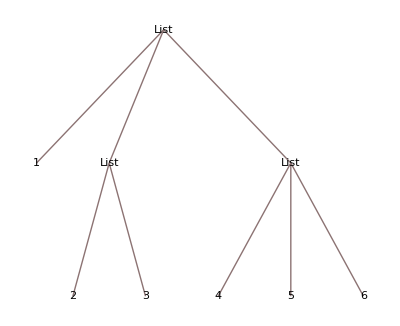

```mathematica
list1//TreeForm
```

Mathematica organizes everything as a list.

```mathematica
human=head[hand,{foot,foot},hand]
```

head[hand,{foot,foot},hand]

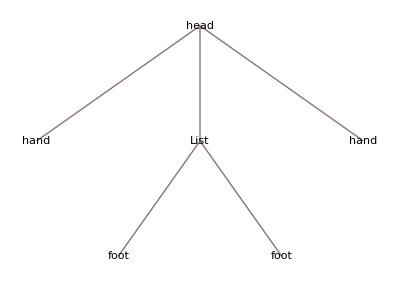

```mathematica
human//TreeForm
```

We can change the leaves in a tree.

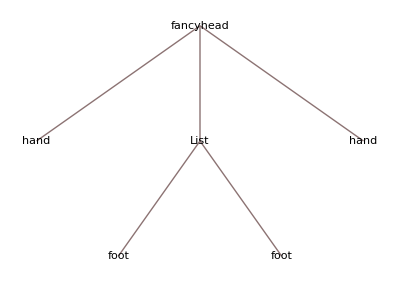

```mathematica
human1=fancyhead@@human//TreeForm
```

Another syntax for this is:

```mathematica
human2=Apply[fancyhead,human]//TreeForm
```

-Graphics-

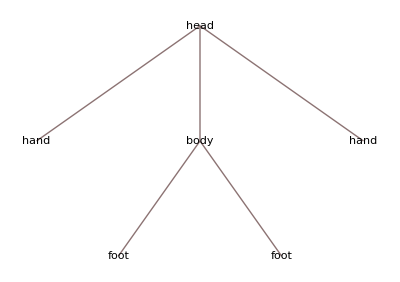

-Graphics-

```mathematica
human3=body@@@human//TreeForm
human4=Apply[body,human,{1}]//TreeForm
```

Apply only corresponds to nodes. This is why our example doesn’t change "hand".

## Simplify When

```mathematica
Simplify[1-Cos[2a]]
```

2 Sin[a]^2

Mathematica always simplifies taking into account the leave count.

{8,6}

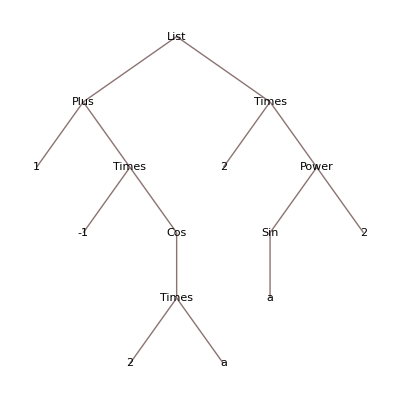

```mathematica
LeafCount/@{1-Cos[2a],2 Sin[a]^2}
TreeForm[{1-Cos[2a],2 Sin[a]^2}]
```

{6,10}

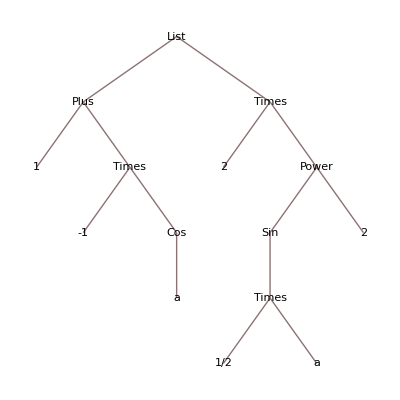

```mathematica
LeafCount/@{1-Cos[a],2 Sin[a/2]^2}
TreeForm[{1-Cos[a],2 Sin[a/2]^2}]
```

## Fraction Mathematica

```mathematica
f[p_/q_]:={p,q};
```

```mathematica
f[(a+2)/(b+3)]
```

{2+a,3+b}

```mathematica
f[1/2]
```

f[1/2]

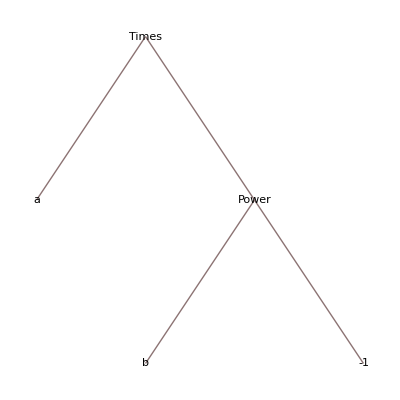

```mathematica
a/b//TreeForm
```

```mathematica
1/2//TreeForm
```

-Graphics-

## Substitutions in Mathematica

```mathematica
(x+4)/(x+5)/.{x->1}
```

5/6

```mathematica
x
```

x

Substitution doesn’t actually replace the value of the character.

```mathematica
rules={a->1,b->2};
```

A very common technique is to write rules in a list.

```mathematica
a+2(b+3)/.rules
```

11

```mathematica
{a,b}/.{a-> b,b-> a}
```

{b,a}

```mathematica
1+x(1+x(1+x))/.{1+x->1}
```

1+x (1+x)

What is going on? Look at the Tree Form.

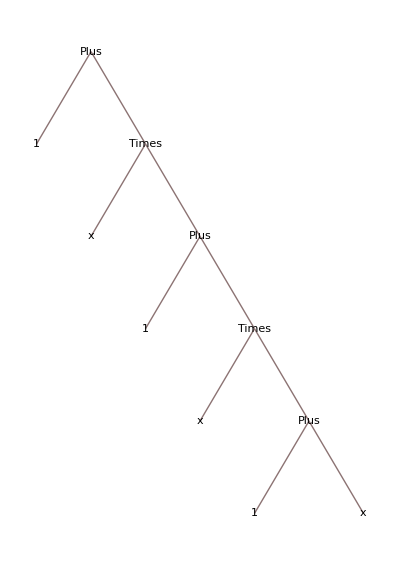

```mathematica
1+x(1+x(1+x))//TreeForm
```

To do the replacement iteratively, put an extra /

```mathematica
1+x(1+x(1+x))//.{1+x->1}
```

1

## Pattern Matching

```mathematica
y=.
```

```mathematica
poly=x^2+x^5+y^4+y^7
```

x^2+x^5+y^4+y^7

```mathematica
poly/.a_^(b_?OddQ)->0
```

x^2+y^4

```mathematica
f[2]+f[2,4]+f[1,3,4]+f[4,5]+f[]/.f[a_]->0
```

f[]+f[2,4]+f[4,5]+f[1,3,4]

```mathematica
f[2]+f[2,4]+f[1,3,4]+f[4,5]+f[]/.f[a__]->0
```

f[]

```mathematica
f[2]+f[2,4]+f[1,3,4]+f[4,5]+f[]/.f[a__,4]->0
```

f[]+f[2]+f[4,5]

```mathematica
f[2]+f[2,4]+f[1,3,4]+f[4,5]+f[]+g[4]/.f[a___]->0
```

g[4]

## Conditions on Functions

```mathematica
fac[n_]:=n fac[n-1];
fac[0]:=1;
```

```mathematica
fac[4]
```

24

```mathematica
fac[0.5]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of fac[-1021.5-1].

Hold[0.5 fac[0.5-1]]

```mathematica
fac1[n_Integer]:=n fac1[n-1];
fac1[0]=1;
```

```mathematica
fac1[3]
```

6

```mathematica
fac1[0.5]
```

fac1[0.5]

```mathematica
fac2[n_Integer]/;n>0:=n fac2[n-2];
fac2[0]:=1;
```

```mathematica
fac2[-3]
```

fac2[-3]

```mathematica
fac2[6]
```

48

```mathematica
bubblesort[before___,a_,b_,after___]/;a>b:=bubblesort[before,b,a,after]
```

```mathematica
bubblesort[1,8,5,9,2,3]
```

bubblesort[1,2,3,5,8,9]

## Efficienty Fib: Timing

## Solving Equations

```mathematica
sol = Solve[a x^2+b x+c== 0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
x/.{sol[[1,1]]}
```

(-b-√(b^2-4 a c))/(2 a)

```mathematica
parameters={a->1,b->3,c->2};
```

```mathematica
x/.{sol[[1,1]]}/.parameters
```

-2

```mathematica
Solve[Sin[a]==1/2,a]
```

{{a→ConditionalExpression[π/6+2 π C[1],C[1]∈ℤ]},{a→ConditionalExpression[(5 π)/6+2 π C[1],C[1]∈ℤ]}}

```mathematica
FindRoot[Log[x]== Exp[x]-5,{x,3}]
```

{x→1.71152}

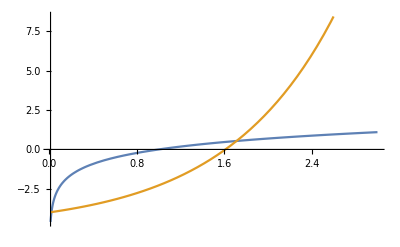

```mathematica
Plot[{Log[x],Exp[x]-5},{x,0.01,3}]
```

```mathematica
DSolve[x''[t]+x[t]==0,x,t]
```

{{x→Function[{t},C[1] Cos[t]+C[2] Sin[t]]}}

```mathematica
DSolve[x''[t]+x'[t]+x[t]==0,x,t]
```

{{x→Function[{t},ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]]}}

```mathematica
DSolve[x''[t]+x'[t]+x[t]==Exp[t],x,t]
```

{{x→Function[{t},ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]+1/3 ⅇ^t (Cos[(√3 t)/2]^2+Sin[(√3 t)/2]^2)]}}

```mathematica
DSolve[x''[t]+x'[t]+x[t]==Exp[Sin[t]],x,t]
```

{{x→Function[{t},ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]+ⅇ^(-t/2) (Sin[(√3 t)/2] (2 ⅇ^(K[1]/2+Sin[K[1]]) Cos[1/2 √3 K[1]])/(√3)K[1]1t+Cos[(√3 t)/2] -(2 ⅇ^(K[2]/2+Sin[K[2]]) Sin[1/2 √3 K[2]])/(√3)K[2]1t)]}}

```mathematica
NDSolve[{x''[t]+x'[t]+x[t]==Exp[Sin[t]],x[0]== 1,x'[0]== 0},x,{t,0,30}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
?NDSolve
```